x^n/(x^n+β^n)

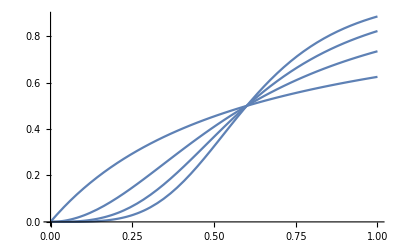

```mathematica
x^n/(x^n+β^n)
Plot[%/.{β->0.6,n->{1,2,3,4}},{x,0,1}]
```

```mathematica
IK=0.012
Kis=1/((1+kX*PIX+kG*kX*kC*GIT*PIX*Paxtot*PaxRatio)*(1+alphaR*RacRatio0)+kG*kX*GIT*PIX);
IKs=IK*(1-Kis*(1+alphaR*RacRatio0));
pars0={alphaR->15,Rtot->7.5,kX->41.7,kG->5.71,kC->5,GIT->0.11,PIX->0.069,Paxtot->3, alphaR->15,LK->5.77}
```

0.012

{alphaR→15,Rtot→7.5,kX→41.7,kG→5.71,kC→5,GIT→0.11,PIX→0.069,Paxtot→3,alphaR→15,LK→5.77}

{alphaR→15,Rtot→7.5,kX→41.7,kG→5.71,kC→5,GIT→0.11,PIX→0.069,Paxtot→3,IK→1}

{alphaR→15,Rtot→7.5,kX→10.7,kG→5.71,kC→5,GIT→0.11,PIX→0.069,Paxtot→3,IK→1}

```mathematica
I0=IKs/IK/.PaxRatio->0//FullSimplify
I1=IKs/IK/.PaxRatio->1//FullSimplify
s1=D[IKs/IK,PaxRatio]/.PaxRatio->1/. RacRatio0->0.2
```

1.-(1. (1+alphaR RacRatio0))/(1+alphaR RacRatio0+kX PIX (1+GIT kG+alphaR RacRatio0))

1.-(1. (1+alphaR RacRatio0))/(GIT kG kX PIX+(1+kX (PIX+GIT kC kG Paxtot PIX)) (1+alphaR RacRatio0))

(1. (1+0.2 alphaR)^2 GIT kC kG kX Paxtot PIX)/(GIT kG kX PIX+(1+0.2 alphaR) (1+kX PIX+GIT kC kG kX Paxtot PIX))^2

(1. (1+0.2 alphaR)^2 GIT kC kG kX Paxtot PIX)/(GIT kG kX PIX+(1+0.2 alphaR) (1+kX PIX+GIT kC kG kX Paxtot PIX))^2

```mathematica
Solve[{I0==a,I1==b, s1==c},{kX,kC,alphaR}]
```

{}

{alphaR→15,Rtot→7.5,kX→5,kG→5.71,kC→15,GIT→0.11,PIX→0.039,Paxtot→3,LK→0.5}

0.012 (1-(1+0.2 alphaR)/(GIT kG kX PIX+(1+0.2 alphaR) (1+kX PIX+GIT kC kG kX PaxRatio Paxtot PIX)))

{0.012 (1-4./(1.80723+4. (3.8773+27.1085 PaxRatio))),0.012 (1-4./(0.12248+4. (1.195+5.51158 PaxRatio)))}

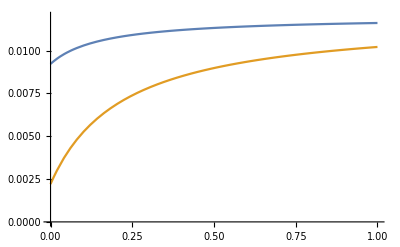

```mathematica
pars={alphaR->15,Rtot->7.5,kX->5,kG->5.71,kC->15,GIT->0.11,PIX->0.039,Paxtot->3,LK->0.5}
IKs/.RacRatio0->0.2
{%/.pars0,%/.pars}
Plot[%,{PaxRatio,0,1},PlotRange->{0,IK}]
```

```mathematica
K= alphaR*RacRatio0*Kis*(1+kX*PIX+kG*kX*kC*Paxtot*GIT*PIX*PaxRatio)
```

(alphaR (1+kX PIX+GIT kC kG kX PaxRatio Paxtot PIX) RacRatio0)/(GIT kG kX PIX+(1+kX PIX+GIT kC kG kX PaxRatio Paxtot PIX) (1+alphaR RacRatio0))

(26.1924 RacRatio0)/(0.12248+1.74616 (1+15 RacRatio0))

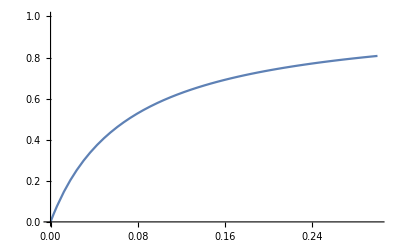

```mathematica
K/.pars/.PaxRatio->0.1
Plot[%,{RacRatio0,0,0.3},PlotRange->{0,1}]
```

{alphaR→15,Rtot→7.5,kX→5,kG→5.71,kC→15,GIT→0.11,PIX→0.039,Paxtot→3,alphaR→15,LK→{0.6}}

{(2.01571×10^8 RacRatio0^4)/((1.80723+7.94357 (1+15 RacRatio0))^4 (1108.42+(2.01571×10^8 RacRatio0^4)/(1.80723+7.94357 (1+15 RacRatio0))^4)),{(845792. RacRatio0^4)/((0.12248+2.02174 (1+15 RacRatio0))^4 (0.1296+(845792. RacRatio0^4)/(0.12248+2.02174 (1+15 RacRatio0))^4))}}

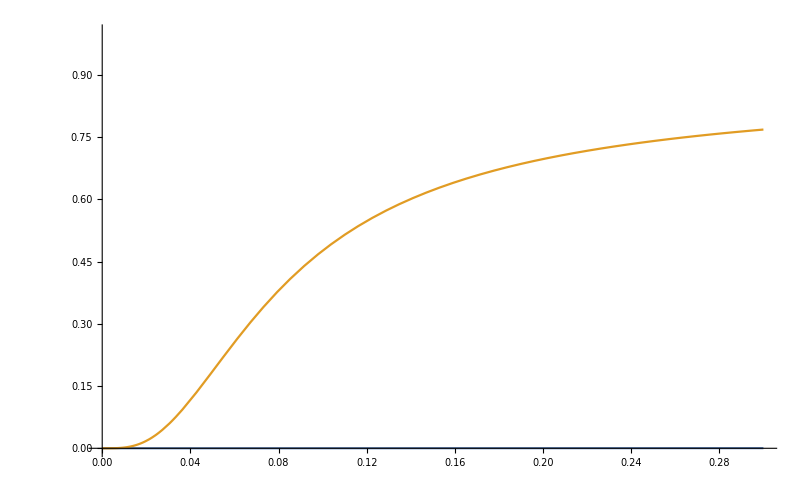

```mathematica
pars={alphaR->15,Rtot->7.5,kX->5,kG->5.71,kC->15,GIT->0.11,PIX->0.039,Paxtot->3, alphaR->15,LK->{0.6}}

K^4/(K^4+LK^4)/.PaxRatio->0.15;
{%/.pars0,%/.pars}
Plot[%,{RacRatio0,0,0.3},PlotRange->{0,1}]
```